```mathematica
Gam[x_,y_]:=-Series[(1-I*(-1-Cos[x]-Cos[y]+(1/4)Cos[2y]-(1/6)Sin[x]Sin[2x])),{x,0,6},{y,0,8}]
```

```mathematica
Gam[x,y]//ExpandAll
```

(-(1+(11 ⅈ)/4)+(ⅈ y^4)/8-(ⅈ y^6)/48+(ⅈ y^8)/640+O[y]^9)+(ⅈ x^2)/6+(17 ⅈ x^4)/72-(179 ⅈ x^6)/2160+O[x]^7

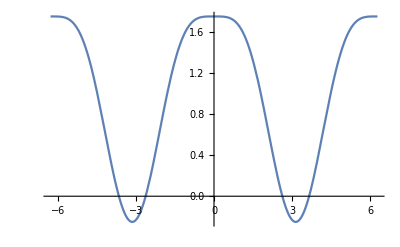

```mathematica
Plot[1+Cos[y]-(1/4)Cos[2y],{y,-2Pi,2Pi}]
```

Note that PhiHat[x,y] must look something like 1 + iP([x,y]) where P is positive homogeneous.

```mathematica
Plot3D[Abs[2+I*(-2-Cos[x]-Cos[y]+(1/4)Cos[2y])],{x,-2Pi,2Pi},{y,-2Pi,2Pi}]
```

-Graphics3D-

```mathematica
RulePhi={Cos[x]->(1/2)(E^(I*x)+E^(-I*x)),
Cos[2x]->(1/2)(E^(2I*x)+E^(-2I*x)),
Cos[y]->(1/2)(E^(I*y)+E^(-I*y)),
Cos[2y]->(1/2)(E^(2I*y)+E^(-2I*y))};
```

```mathematica
PhiHat[x_,y_]:=(1-I*(-1+11/4-Cos[x]-Cos[y]+(1/4)Cos[2y]-(1/6)Sin[x]Sin[2x]))
```

```mathematica
PhiHat[0,0]
```

1

```mathematica
Series[Log[PhiHat[x,y]/PhiHat[0,0]],{x,0,4},{y,0,6}]
```

((ⅈ y^4)/8-(ⅈ y^6)/48+O[y]^7)+((5 ⅈ)/2+(5 y^4)/16-(5 y^6)/96+O[y]^7) x^2+((25/8-(41 ⅈ)/24)-(41/192+(25 ⅈ)/32) y^4+(41/1152+(25 ⅈ)/192) y^6+O[y]^7) x^4+O[x]^5

```mathematica
Plot3D[Abs[(1+I*(0.5+(3/4)Cos[x]-Cos[y]+(1/4)Cos[2y]))],{x,-2Pi,2Pi},{y,-2Pi,2Pi}]
```

-Graphics3D-

```mathematica
PhiHat[0,0]
```

(4-11 ⅈ)/(√137)

```mathematica
PhiHatNew[x_,y_]:=PhiHat[x,y]/PhiHat[0,0];
```

```mathematica
Plot3D[Abs[PhiHat[x,y]],{x,-2Pi,2Pi},{y,-2Pi,2Pi}]
```

-Graphics3D-

```mathematica
Series[Log[PhiHatNew[x,y]],{x,0,3},{y,0,6}]//Simplify
```

(-(11/274-(2 ⅈ)/137) y^4+(11/1644-ⅈ/411) y^6+O[y]^7)+(-(22/137-(8 ⅈ)/137)-(105/18769-(88 ⅈ)/18769) y^4+(35/37538-(44 ⅈ)/56307) y^6+O[y]^7) x^2+O[x]^4

Note that we must normalize by a real number so as not to introduce “real impurities”

```mathematica
Abs[PhiHat[0,0]]
```

1

```mathematica
PhiHat[x,y]/.RulePhi//ExpandAll
```

(1+(7 ⅈ)/4)-1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)-1/2 ⅈ ⅇ^(-ⅈ y)-1/2 ⅈ ⅇ^(ⅈ y)+1/8 ⅈ ⅇ^(-2 ⅈ y)+1/8 ⅈ ⅇ^(2 ⅈ y)

```mathematica
PhiHat[0,0]
```

1

```mathematica
(1+(7 ⅈ)/4)-1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)-1/2 ⅈ ⅇ^(-ⅈ y)-1/2 ⅈ ⅇ^(ⅈ y)+1/8 ⅈ ⅇ^(-2 ⅈ y)+1/8 ⅈ ⅇ^(2 ⅈ y)
```

(1+(7 ⅈ)/4)-1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)-1/2 ⅈ ⅇ^(-ⅈ y)-1/2 ⅈ ⅇ^(ⅈ y)+1/8 ⅈ ⅇ^(-2 ⅈ y)+1/8 ⅈ ⅇ^(2 ⅈ y)

```mathematica
Series[Log[PhiHat[x,y]],{x,0,4},{y,0,6}]
```

((ⅈ y^4)/8-(ⅈ y^6)/48+O[y]^7)+(ⅈ/2+y^4/16-y^6/96+O[y]^7) x^2+((1/8-ⅈ/24)-(1/192+ⅈ/32) y^4+(1/1152+ⅈ/192) y^6+O[y]^7) x^4+O[x]^5

```mathematica
FourierSeries[E^(I*(x^2+y^4)),{x,y},{2,4}]
```

$Aborted

Let us try again...

```mathematica
x=.;y=.
```

```mathematica
Lg[x,y]:=Series[2-(I/2)*Sin[x]^2-Sin[x]^4 -(I/2)*Sin[y]^4-Sin[y]^8,{x,0,6},{y,0,8}]
```

```mathematica
Lg[x,y]
```

(2-(ⅈ y^4)/2+(ⅈ y^6)/3-(1+ⅈ/10) y^8+O[y]^9)-(ⅈ x^2)/2-(1-ⅈ/6) x^4+(2/3-ⅈ/45) x^6+O[x]^7

```mathematica
PhiH[x_,y_]:=(2-(I/2)*Sin[x/2]^2-Sin[x/2]^4 -(I/2)*Sin[y/2]^4-Sin[y/2]^8)/2
```

```mathematica
PhiH[x,y]
```

1/2 (2-1/2 ⅈ Sin[x/2]^2-Sin[x/2]^4-1/2 ⅈ Sin[y/2]^4-Sin[y/2]^8)

```mathematica
PhiH[0,0]
```

1

```mathematica
Series[Log[PhiH[x,y]/PhiH[0,0]],{x,0,4},{y,0,6}]
```

(-(ⅈ y^4)/64+(ⅈ y^6)/384+O[y]^7)+(-ⅈ/16+y^4/1024-y^6/6144+O[y]^7) x^2+(-(15/512-ⅈ/192)-(1/12288+(7 ⅈ)/16384) y^4+(1/73728+(7 ⅈ)/98304) y^6+O[y]^7) x^4+O[x]^5

```mathematica
Plot3D[Abs[PhiH[x,y]],{x,-2Pi,2Pi},{y,-2Pi,2Pi}]
```

-Graphics3D-

```mathematica
RulePhi={Sin[x/2]->(1/(2I))(E^(I*x/2)-E^(-I*x/2)),
Sin[y/2]-> (1/(2I))(E^(I*y/2)-E^(-I*y/2))};
```

```mathematica
PhiH[x,y]/.RulePhi//ExpandAll
```

(173/256-(7 ⅈ)/32)+(1/8+ⅈ/16) ⅇ^(-ⅈ x)+(1/8+ⅈ/16) ⅇ^(ⅈ x)-1/32 ⅇ^(-2 ⅈ x)-1/32 ⅇ^(2 ⅈ x)+(7/64+ⅈ/16) ⅇ^(-ⅈ y)+(7/64+ⅈ/16) ⅇ^(ⅈ y)-(7/128+ⅈ/64) ⅇ^(-2 ⅈ y)-(7/128+ⅈ/64) ⅇ^(2 ⅈ y)+1/64 ⅇ^(-3 ⅈ y)+1/64 ⅇ^(3 ⅈ y)-1/512 ⅇ^(-4 ⅈ y)-1/512 ⅇ^(4 ⅈ y)

```mathematica
PhiHCx[x_,y_]:=(3-(I/2)*Sin[x/2]^2-Sin[x/2]^4 -(I/2)*Sin[y/2]^4-Sin[y/2]^8-(I/16)*(Sin[x]Cos[y] -Sin[x]) )/3
```

```mathematica
Series[PhiHCx[x,y],{x,0,4},{y,0,6}]
```

(1-(ⅈ y^4)/96+(ⅈ y^6)/576+O[y]^7)+((ⅈ y^2)/96-(ⅈ y^4)/1152+(ⅈ y^6)/34560+O[y]^7) x-(ⅈ x^2)/24+(-(ⅈ y^2)/576+(ⅈ y^4)/6912-(ⅈ y^6)/207360+O[y]^7) x^3-(1/48-ⅈ/288) x^4+O[x]^5

```mathematica
PhiHCx[0,0]
```

1

```mathematica
Series[Log[PhiHCx[x,y]/PhiHCx[0,0]],{x,0,2},{y,0,4}]
```

(-(ⅈ y^4)/96+O[y]^5)+((ⅈ y^2)/96-(ⅈ y^4)/1152+O[y]^5) x+(-ⅈ/24+y^4/2048+O[y]^5) x^2+O[x]^3

```mathematica
Show[Plot3D[1.003Abs[PhiHCx[x,y]],{x,-3Pi,3Pi},{y,-3Pi,3Pi}],Plot3D[1,{x,-3Pi,3Pi},{y,-3Pi,3Pi}, PlotStyle-> {Black}]]
```

-Graphics3D-

```mathematica
RulePhiCx={Sin[x/2]->(1/(2I))(E^(I*x/2)-E^(-I*x/2)),
Sin[y/2]-> (1/(2I))(E^(I*y/2)-E^(-I*y/2)),
Sin[x]Sin[y/2]^2-> (1/(2I))(E^(I*x)-E^(-I*x))(1/(2I))(E^(I*y/2)-E^(-I*y/2))(1/(2I))(E^(I*y/2)-E^(-I*y/2)),
Sin[x]->(1/(2I))(E^(I*x)-E^(-I*x)),
Cos[y]-> (1/(2))(E^(I*y)+E^(-I*y))};
```

```mathematica
PhiHCx[x,y]/.RulePhiCx//ExpandAll
```

(301/384-(7 ⅈ)/48)+(7/96+ⅈ/24) ⅇ^(-ⅈ x)+(3/32+ⅈ/24) ⅇ^(ⅈ x)-1/48 ⅇ^(-2 ⅈ x)-1/48 ⅇ^(2 ⅈ x)+1/192 ⅇ^(-ⅈ x-ⅈ y)-1/192 ⅇ^(ⅈ x-ⅈ y)+1/192 ⅇ^(-ⅈ x+ⅈ y)-1/192 ⅇ^(ⅈ x+ⅈ y)+(7/96+ⅈ/24) ⅇ^(-ⅈ y)+(7/96+ⅈ/24) ⅇ^(ⅈ y)-(7/192+ⅈ/96) ⅇ^(-2 ⅈ y)-(7/192+ⅈ/96) ⅇ^(2 ⅈ y)+1/96 ⅇ^(-3 ⅈ y)+1/96 ⅇ^(3 ⅈ y)-1/768 ⅇ^(-4 ⅈ y)-1/768 ⅇ^(4 ⅈ y)

```mathematica
(3-(I/2)*Sin[x/2]^2-Sin[x/2]^4 -(I/2)*Sin[y/2]^4-Sin[y/2]^8-(I/16)*(Sin[x]Cos[y] -Sin[x]) )*(3+(I/2)*Sin[x/2]^2-Sin[x/2]^4 +(I/2)*Sin[y/2]^4-Sin[y/2]^8+(I/16)*(Sin[x]Cos[y] -Sin[x]) )//ExpandAll//Simplify
```

1/64 (576+64 Sin[x/2]^8-8 Sin[x/2]^2 (-2+2 Cos[y]+Sin[x]) Sin[y/2]^2+Sin[x]^2 Sin[y/2]^4-8 Sin[x] Sin[y/2]^6-368 Sin[y/2]^8+64 Sin[y/2]^16+16 Sin[x/2]^4 (-23+8 Sin[y/2]^8))

```mathematica
Plot3D[1/64 (576+64 Sin[x/2]^8-8 Sin[x/2]^2 (-2+2 Cos[y]+Sin[x]) Sin[y/2]^2+Sin[x]^2 Sin[y/2]^4-8 Sin[x] Sin[y/2]^6-368 Sin[y/2]^8+64 Sin[y/2]^16+16 Sin[x/2]^4 (-23+8 Sin[y/2]^8)),{x,-Pi-0.1,Pi+0.1},{y,-Pi-1,Pi+1}]
```

-Graphics3D-

Look at Gradient...

```mathematica
G[x_,y_]:=1/64 (576+64 Sin[x/2]^8-8 Sin[x/2]^2 (-2+2 Cos[y]+Sin[x]) Sin[y/2]^2+Sin[x]^2 Sin[y/2]^4-8 Sin[x] Sin[y/2]^6-368 Sin[y/2]^8+64 Sin[y/2]^16+16 Sin[x/2]^4 (-23+8 Sin[y/2]^8))
```

```mathematica
GR[x_,y_]=Grad[G[x,y],{x,y}]//Simplify
```

{1/32 (64 Sin[x/2]^6 Sin[x]-1/2 (-2+2 Cos[y]+Sin[x]) (Cos[x] (-1+Cos[y])+4 Sin[x]) Sin[y/2]^2-4 Sin[x/2]^2 (Cos[x] Sin[y/2]^2+Sin[x] (46-16 Sin[y/2]^8))),1/64 (-4 Sin[x/2]^2 (-4+4 Cos[y]+Sin[x])+256 Sin[x/2]^4 Sin[y/2]^6+Sin[y/2]^2 (Sin[x]^2-12 Sin[x] Sin[y/2]^2+32 Sin[y/2]^4 (-23+8 Sin[y/2]^8))) Sin[y]}

```mathematica
GR[0.0,0]
```

{0.,0.}

```mathematica
Show[Plot3D[-0.01+Norm[GR[x,y]],{x,-3Pi,3Pi},{y,-3Pi,3Pi}],Plot3D[0,{x,-3Pi,3Pi},{y,-3Pi,3Pi},PlotStyle->{Black}]]
```

-Graphics3D-

```mathematica
Plot3D[1/64 (576+64 Sin[x/2]^8-8 Sin[x/2]^2 (-2+2 Cos[y]+Sin[x]) Sin[y/2]^2+Sin[x]^2 Sin[y/2]^4-8 Sin[x] Sin[y/2]^6-368 Sin[y/2]^8+64 Sin[y/2]^16+16 Sin[x/2]^4 (-23+8 Sin[y/2]^8)),{x,-3Pi,3Pi},{y,-3Pi,3Pi}]
```

-Graphics3D-

```mathematica
Plot3D[1/4 (-Sin[x/2]^2 (-1+Cos[y]+2 Sin[x])+4 Sin[x]^2 Sin[y/2]^2-6 Sin[x] Sin[y/2]^4+16 Sin[x/2]^4 Sin[y/2]^6+2 Sin[y/2]^6 (-23+8 Sin[y/2]^8)) Sin[y],{x,-3Pi,3Pi},{y,-3Pi,3Pi}]
```

-Graphics3D-

```mathematica
Plot3D[y^4/96-x*y^2/96+x^2/24,{x,-20,20},{y,-20,20}]
```

-Graphics3D-

```mathematica
Plot3D[Cos[(-10x/(100^(1/2))-10y/(100^(1/4))-y^4/96+y^2*x/96-x^2/24)],{x,-20,20},{y,-20,20}]
```

-Graphics3D-

```mathematica
For[i=0,i<4,i++,Print[NIntegrate[Cos[-i*x-i*y+x^4/96-x^2*y/96+y^2/24],{x,-40,40},{y,-40,40}, Method->"OscillatorySelection"]]]
```

19.0448

-5.4534

6.86186

-4.35529

```mathematica
out=Table[{i,i,NIntegrate[Cos[i*x+1*y+x^4/96-x^2*y/96+y^2/24],{x,-10,10},{y,-10,10}, PrecisionGoal -> 4,Method->"OscillatorySelection"]},{i,-4,4,1}]
Export["C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/data.txt",out,"Table","FieldSeparators"->" "];
```

{{-4,-4,-7.561},{-3,-3,5.61084},{-2,-2,-3.09496},{-1,-1,5.87289},{0,0,-4.11363},{1,1,5.87289},{2,2,-3.09496},{3,3,5.61084},{4,4,-7.56092}}

```mathematica
NIntegrate[Cos[10*x+1*y+x^4/96-x^2*y/96+y^2/24],{x,-10,10},{y,-10,10}, PrecisionGoal -> 4,Method->"OscillatorySelection",EvaluationMonitor:>((errors=Through[#1@"Error"])&)]
Total@errors
```

-6.60668

0.000232224

```mathematica
H[i_,j_]:=NIntegrate[Cos[(-i*x/(100^(1/2))-j*y/(100^(1/4))-y^4/96+y^2*x/96-x^2/24)],{x,-11,11},{y,-11,11}, PrecisionGoal -> 4,Method->"OscillatorySelection"]
data=Flatten[Table[{i,j,H[i,j]},{i,-7,7,0.1},{j,-7,7,0.1}],1];
Export["C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/data4.csv",data,"CSV"]
```

C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/data4.csv

```mathematica
ListPlot3D[data,ColorFunction->Hue,PlotRange->Full]
```

-Graphics3D-

```mathematica
H[i_,j_]:=NIntegrate[Cos[(-i*x/(100^(1/2))-j*y/(100^(1/4))-y^4/96+y^2*x/96-x^2/24)],{x,-11,11},{y,-11,11}, PrecisionGoal -> 4,Method->"OscillatorySelection"]
data=Flatten[Table[{i,j,H[i,j]},{i,-7,7,0.1},{j,-10,7,0.1}],1];
Export["C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/data6.csv",data,"CSV"]
```

C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/data5.csv

```mathematica
ListPlot3D[Import["C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/data_concatenate.csv"],ColorFunction->Hue,PlotRange->Full]
```

-Graphics3D-